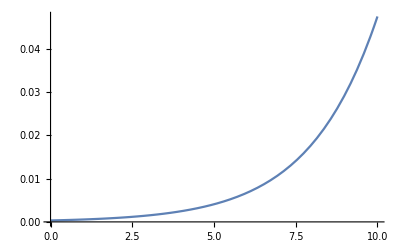

```mathematica
avgk = 8;
trophicload=2;
probext = 1/(1 + Exp[-0.5*(Np-(trophicload*avgk))]);
Plot[probext,{Np,0,10}]
```

10

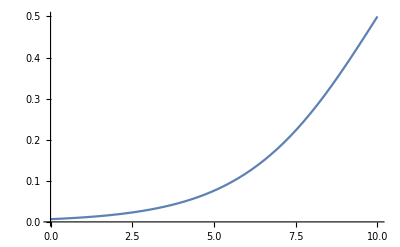

```mathematica
tl=10
probext2 = 1/(1 + Exp[-0.5*(Np-tl)]);
Plot[probext2,{Np,0,10}]
```

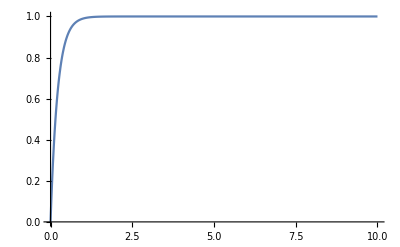

```mathematica
Plot[1-0.01^n-(1-0.01)^1000,{n,0,10},PlotRange->{0,1}]
```

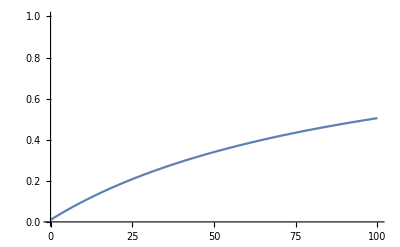

```mathematica
baseline=0.01;
Plot[baseline+ (1-baseline)*(1 - 1/(1+0.01n)),{n,0,100},PlotRange->{0,1}]
```

```mathematica
Solve[{
0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,P1,P2,R1,R2}]
```

{{R→0,P1→0,P2→0,R1→1,R2→1},{R→1,P1→0,P2→0,R1→0,R2→0},{R→1,P1→0,P2→0,R1→1,R2→0},{R→1,P1→0,P2→0,R1→1,R2→1},{R→0,P1→0,P2→0,R1→1,R2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→0,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→1,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→0,R2→0},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→1,R2→0},{R→1,P1→0,P2→0,R1→0,R2→1},{R→0,P1→0,P2→0,R1→0,R2→1},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→0},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→1},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→0},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→1},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→1,R2→m2/(a2 e2)},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→1},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→0},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→((a2 e2-m2) r2)/(a2^2 e2),R1→m1/(a1 e1),R2→m2/(a2 e2)},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→0,R2→m2/(a2 e2)},{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))},{R→m1/(a1 e1),P1→-(-a1 a2 e1 e2 r+a2 e2 m1 r+a1 a2 e1 e2 r2+a2 e2 m1 r2-a1 e1 m2 r2)/(a1^2 a2 e1 e2),P2→((a1 a2 e1 e2+a2 e2 m1-a1 e1 m2) r2)/(a1 a2^2 e1 e2),R1→0,R2→-(a2 e2 m1-a1 e1 m2)/(a1 a2 e1 e2)},{R→m2/(a2 e2),P1→((a1 a2 e1 e2-a2 e2 m1+a1 e1 m2) r1)/(a1^2 a2 e1 e2),P2→-(-a1 a2 e1 e2 r+a1 e1 m2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 e1 m2 r1)/(a1 a2^2 e1 e2),R1→-(-a2 e2 m1+a1 e1 m2)/(a1 a2 e1 e2),R2→0},{R→0,P1→0,P2→0,R1→0,R2→0}}

```mathematica
FullSimplify[{R->-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1->(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2->((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1->-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2->-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))}]
```

{R→(a2 e2 m1 r1+a1 e1 (a2 e2 (r-r1-r2)+m2 r2))/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (-a2 e2 m1 (r+r2)+a1 e1 (2 a2 e2 r+m2 r2)))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((a2 e2 m1 r1+a1 e1 (2 a2 e2 r-m2 (r+r1))) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→(a2 e2 m1 (r+r2)+a1 e1 (-m2 r2+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2)),R2→(-a2 e2 m1 r1+a1 e1 (m2 (r+r1)+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2))}

```mathematica
SolP = Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R/k)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1/k1)-a1*R1*P1,
0 == r2*R2*(1-R2/k2)-a2*R2*P2
},{R,R1,R2}]
```

{{R→0,R1→0,R2→0},{R→(-a1 k P1-a2 k P2+k r)/r,R1→0,R2→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0},{R→(-a1 k P1-a2 k P2+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2},{R→(-a1 k P1-a2 k P2+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2},{R→(-a1 k P1-a2 k P2+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2}}

```mathematica
SolP = Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R/k)-a1*R*P1-a2*R*P2 -a3*R*P3,
0 == r1*R1*(1-R1/k1)-a1*R1*P1,
0 == r2*R2*(1-R2/k2)-a2*R2*P2,
0 == r3*R3*(1-R3/k3)-a3*R3*P3
},{R,R1,R2,R3}]
```

{{R→0,R1→0,R2→0,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→0,R3→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→0},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→0},{R→0,R1→0,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→0,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→0,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→0,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3},{R→(-a1 k P1-a2 k P2-a3 k P3+k r)/r,R1→(-a1 k1 P1+k1 r1)/r1,R2→(-a2 k2 P2+k2 r2)/r2,R3→(-a3 k3 P3+k3 r3)/r3}}

```mathematica
Factor[(-a1 k P1-a2 k P2-a3 k P3+k r)/r]
```

(k (-a1 P1-a2 P2-a3 P3+r))/r

```mathematica
Solve[(k (-m*P+r))/r==1-m*ϵ,ϵ]
```

{{ϵ→(k m P+r-k r)/(m r)}}

```mathematica
FullSimplify[(-k m P+r-k r)/(m r)]
```

(r-k (m P+r))/(m r)

```mathematica
FullSimplify[SolP[[8]]]
```

{R→(-a1 P1-a2 P2+r)/r,R1→1-(a1 P1)/r1,R2→1-(a2 P2)/r2}

```mathematica
Sol=Solve[{
0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,R1,R2,P1,P2}]
```

{{R→0,R1→1,R2→1,P1→0,P2→0},{R→1,R1→0,R2→0,P1→0,P2→0},{R→1,R1→1,R2→0,P1→0,P2→0},{R→1,R1→1,R2→1,P1→0,P2→0},{R→0,R1→1,R2→0,P1→0,P2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),R1→1,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2))},{R→m2/(a2 e2),R1→1,R2→0,P1→0,P2→((a2 e2-m2) r)/(a2^2 e2)},{R→1,R1→0,R2→1,P1→0,P2→0},{R→0,R1→0,R2→1,P1→0,P2→0},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→1,P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0},{R→m1/(a1 e1),R1→0,R2→1,P1→((a1 e1-m1) r)/(a1^2 e1),P2→0},{R→0,R1→1,R2→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→0,R1→m1/(a1 e1),R2→1,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0},{R→0,R1→m1/(a1 e1),R2→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0},{R→0,R1→m1/(a1 e1),R2→m2/(a2 e2),P1→((a1 e1-m1) r1)/(a1^2 e1),P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→0,R1→0,R2→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2)},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→0,P1→(r (2 a1 e1 r1-m1 r1))/(a1^2 e1 (r+r1)),P2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),R1→0,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2))},{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2))},{R→m1/(a1 e1),R1→0,R2→0,P1→((a1 e1-m1) r)/(a1^2 e1),P2→0},{R→m1/(a1 e1),R1→0,R2→-(a2 e2 m1-a1 e1 m2)/(a1 a2 e1 e2),P1→-(-a1 a2 e1 e2 r+a2 e2 m1 r+a1 a2 e1 e2 r2+a2 e2 m1 r2-a1 e1 m2 r2)/(a1^2 a2 e1 e2),P2→((a1 a2 e1 e2+a2 e2 m1-a1 e1 m2) r2)/(a1 a2^2 e1 e2)},{R→m2/(a2 e2),R1→0,R2→0,P1→0,P2→((a2 e2-m2) r)/(a2^2 e2)},{R→m2/(a2 e2),R1→-(-a2 e2 m1+a1 e1 m2)/(a1 a2 e1 e2),R2→0,P1→((a1 a2 e1 e2-a2 e2 m1+a1 e1 m2) r1)/(a1^2 a2 e1 e2),P2→-(-a1 a2 e1 e2 r+a1 e1 m2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 e1 m2 r1)/(a1 a2^2 e1 e2)},{R→0,R1→0,R2→0,P1→0,P2→0}}

```mathematica
internalsolution = Sol[[19]]
```

{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2))}

```mathematica
FullSimplify[-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2))]
```

```mathematica
(a2 e2 m1 r1+a1 e1 (a2 e2 (r-r1-r2)+m2 r2))/(a1 a2 e1 e2 (r+r1+r2))/.{a2->a1,e2->e1,r2->r,r1->r,m2->m1}
```

(a1 e1 m1 r+a1 e1 (-a1 e1 r+m1 r))/(3 a1^2 e1^2 r)

```mathematica
FullSimplify[%]
```

-1/3+(2 m1)/(3 a1 e1)

Is the internal equilibrium stable?
Answer: given particular parameter values, it can be :) (at higher conversion efficiencies and high resource growth rates)

```mathematica
f = { e1*a1*(R+R1)*P1-m1*P1,
e2*a2*(R+R2)*P2-m2*P2,
 r*R*(1-R)-a1*R*P1-a2*R*P2,
 r1*R1*(1-R1)-a1*R1*P1,
 r2*R2*(1-R2)-a2*R2*P2};
x = {P1,P2,R,R1,R2};
```

```mathematica
Jac = D[f,{x}]/.internalsolution;
```

```mathematica
Manipulate[
Eig = N[Eigenvalues[Jac]/.{e1->E1,e2->E2,m1->M1,m2->M2,a1->A1,a2->A2,r->R,r1->R1,r2->R2}];
REig= Re[Eig];
ImEig = Im[Eig];
(*ListPlot[Transpose[{REig,ImEig}]],*)
Max[REig],
{E1,0.1,1},{E2,0.1,1},{M1,0.1,1},{M2,0.1,1},{A1,0.1,1},{A2,0.1,1},{R,0.1,3},{R1,0.1,3},{R2,0.1,3}
]
```

```mathematica
|
```

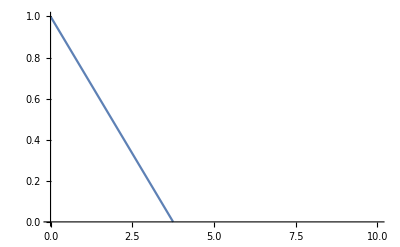

```mathematica
Nstar =1 - (numpred*a*P)/r;
Plot[Nstar/.{P->0.1,r->0.3,a->0.8},{numpred,0,10},PlotRange->{0,1}]
```

```mathematica
PrExt= Probability[-Infinity<x<0,x\[Distributed] NormalDistribution[μ,σ]]
PrExtspecific = PrExt/.μ->(1-n*ϵ)
```

1/2 Erfc[μ/(√2 σ)]

1/2 Erfc[(1-n ϵ)/(√2 σ)]

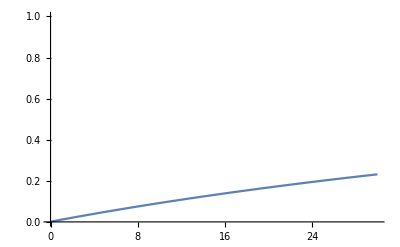

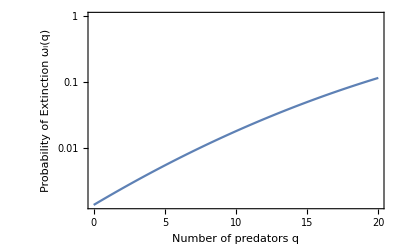

```mathematica
Plot[(ϵ*n+pb)/(1+ϵ*n)/.{pb->0.001,ϵ->0.01},{n,0,30},PlotRange->{0,1}]
PrExtPlot = LogPlot[PrExt/.{μ->1-n*ϵ/.{ϵ->0.03},σ->1/3},{n,0,20},PlotRange->{PrExtspecific/.{σ->1/3,ϵ->0.03,n->0},1},Frame->True,FrameLabel->{"Number of predators q","Probability of Extinction ω_i(q)"}]
```

```mathematica
Export["~/Dropbox/Postdoc/2014_Lego/Anime/figures/extinction.pdf",PrExtPlot]
```

~/Dropbox/Postdoc/2014_Lego/Anime/figures/extinction.pdf

1/2 Erfc[(1-n ϵ)/(√2 σ)]

```mathematica
PrExtspecific/.{σ->1/3,ϵ->0.03,n->0}
```

0.0013499

```mathematica
PrExt/.{μ->1-0*ϵ/.{ϵ->0.05},σ->0.33}
```

0.00122154

```mathematica
Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,R1,R2}]
```

```mathematica
Conn =FullSimplify[(pi(pa/(pa+pn+pi))+pa(pi/(pa+pi+pn))) + (pn(pa/(pa+pn+pi+pm))+pa(pn/(pa+pi+pn))) + (pa(pa/(pi+pn+pa)))/.{pi->1-pa+pn+pm}]
```

1/2 (4 pa+(pa (1-2 pa+pm))/(1+pm+2 pn)-(pa+2 pa pm)/(1+2 pm+2 pn))

```mathematica
Plot3D[Conn/.{pm->0.01},{pa,0,1},{pn,0,1},AxesLabel->{"pa","pn"}]
```

-Graphics3D-

```mathematica
PrExt= Probability[-Infinity<x<0,x\[Distributed] NormalDistribution[μ,σ]]
PrExtspecific = PrExt/.μ->ζ/q
```

1/2 Erfc[μ/(√2 σ)]

1/2 Erfc[ζ/(√2 q σ)]

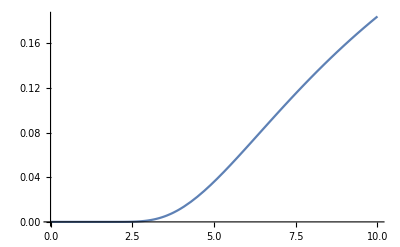

```mathematica
Plot[PrExtspecific/.{ζ->3,σ->1/3},{q,0,10}]
```

```mathematica
PrExtspecific = PrExt/.{σ->1,μ->1-q}
```

1/2 Erfc[(1-q)/(√2)]

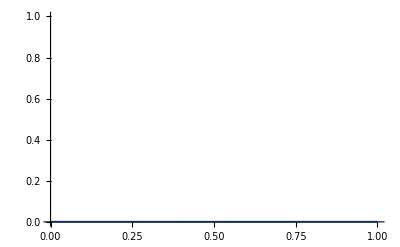

```mathematica
Plot[1/2 Erfc[(1-(1/8)q)/(√0.1)],{q,0,1},PlotRange->{0,1}]
```

```mathematica
PrExtspecific/.{ζ->3,σ->1/3,q->0}
```

Erfc[ComplexInfinity]/2

```mathematica
SolP = Solve[{
0 ==a*b*R*P - m*P,
0 ==(a1*b1*R1*P1 + a2+b2+R2+P1)  - m1*P1
},{R,R1}]
```

{{R→m/(a b),R1→(-a2-b2-P1+m1 P1-R2)/(a1 b1 P1)}}

```mathematica
(*No Sharing*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r1*R1*(1-R1/k1)-a1*R1*P1,
0==r2*R2*(1-R2/k2)-a2*R2*P1,
0 == a*R*P- m*P,
0 == a1*R1*P1+a2*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→k,R1→0,R2→k2,P→0,P1→0},{R→k,R1→k1,R2→0,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→k1,R2→k2,P→0,P1→0},{R→0,R1→0,R2→0,P→0,P1→0},{R→0,R1→0,R2→k2,P→0,P1→0},{R→0,R1→k1,R2→k2,P→0,P1→0},{R→0,R1→k1,R2→0,P→0,P1→0},{R→m/a,R1→k1,R2→k2,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→0,R2→k2,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→k1,R2→0,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→0,R2→0,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→0,R2→m1/a2,P→((a k-m) r)/(a^2 k),P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→m/a,R1→m1/a1,R2→0,P→((a k-m) r)/(a^2 k),P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→k,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→0,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→k,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→(r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2)},{R→0,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→(r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2)},{R→m/a,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→((a k-m) r)/(a^2 k),P1→(r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2)},{R→k,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→0,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)}}

```mathematica
(*50% Sharing*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r1*R1*(1-R1/k1)-a1*R1*P1-a12*R1*P,
0==r2*R2*(1-R2/k2)-a2*R2*P1,
0 == a*R*P+ a12*R1*P- m*P,
0 == a1*R1*P1+a2*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→0,R1→k1,R2→0,P→0,P1→0},{R→k,R1→0,R2→k2,P→0,P1→0},{R→k,R1→k1,R2→0,P→0,P1→0},{R→k,R1→k1,R2→k2,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→((a1 k1 r1+a2 k2 r1-m1 r1) r2)/(a2^2 k2 r1+a1^2 k1 r2)},{R→k,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→0,R1→k1,R2→k2,P→0,P1→0},{R→0,R1→0,R2→0,P→0,P1→0},{R→0,R1→0,R2→k2,P→0,P1→0},{R→0,R1→m/a12,R2→k2,P→((a12 k1-m) r1)/(a12^2 k1),P1→0},{R→-(-a12^2 k k1 r+a a12 k k1 r1-a k m r1)/(a12^2 k1 r+a^2 k r1),R1→-(a a12 k k1 r-a12 k1 m r-a^2 k k1 r1)/(a12^2 k1 r+a^2 k r1),R2→k2,P→(r (a k r1+a12 k1 r1-m r1))/(a12^2 k1 r+a^2 k r1),P1→0},{R→0,R1→m/a12,R2→0,P→((a12 k1-m) r1)/(a12^2 k1),P1→0},{R→0,R1→m/a12,R2→-(a1 m-a12 m1)/(a12 a2),P→-(-a12 a2^2 k1 k2 r1+a2^2 k2 m r1+a1 a12 a2 k1 k2 r2+a1^2 k1 m r2-a1 a12 k1 m1 r2)/(a12^2 a2^2 k1 k2),P1→((a12 a2 k2+a1 m-a12 m1) r2)/(a12 a2^2 k2)},{R→-(-a12^2 k k1 r+a a12 k k1 r1-a k m r1)/(a12^2 k1 r+a^2 k r1),R1→-(a a12 k k1 r-a12 k1 m r-a^2 k k1 r1)/(a12^2 k1 r+a^2 k r1),R2→0,P→(r (a k r1+a12 k1 r1-m r1))/(a12^2 k1 r+a^2 k r1),P1→0},{R→-((-a12^2 a2^2 k k1 k2 r+a a12 a2^2 k k1 k2 r1-a a2^2 k k2 m r1-a a1 a12 a2 k k1 k2 r2-a a1^2 k k1 m r2+a a1 a12 k k1 m1 r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)),R1→-(a a12 a2^2 k k1 k2 r-a12 a2^2 k1 k2 m r-a^2 a2^2 k k1 k2 r1+a^2 a1 a2 k k1 k2 r2-a^2 a1 k k1 m1 r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2),R2→-((-a a1 a12 a2 k k1 k2 r+a1 a12 a2 k1 k2 m r-a12^2 a2 k1 k2 m1 r+a^2 a1 a2 k k1 k2 r1-a^2 a2 k k2 m1 r1-a^2 a1^2 k k1 k2 r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)),P→(r (a a2^2 k k2 r1+a12 a2^2 k1 k2 r1-a2^2 k2 m r1+a a1^2 k k1 r2-a1 a12 a2 k1 k2 r2-a1^2 k1 m r2+a1 a12 k1 m1 r2))/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2),P1→((-a a1 a12 k k1 r+a12^2 a2 k1 k2 r+a1 a12 k1 m r-a12^2 k1 m1 r+a^2 a1 k k1 r1+a^2 a2 k k2 r1-a^2 k m1 r1) r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)},{R→k,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→m/a,R1→0,R2→k2,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→0,R2→0,P→((a k-m) r)/(a^2 k),P1→0},{R→m/a,R1→0,R2→m1/a2,P→((a k-m) r)/(a^2 k),P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→0,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→0,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→((a1 k1 r1+a2 k2 r1-m1 r1) r2)/(a2^2 k2 r1+a1^2 k1 r2)},{R→0,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→-(-a1 m+a12 m1)/(a a1),R1→m1/a1,R2→0,P→((a a1 k-a1 m+a12 m1) r)/(a^2 a1 k),P1→-(a a1 a12 k k1 r-a1 a12 k1 m r+a12^2 k1 m1 r-a^2 a1 k k1 r1+a^2 k m1 r1)/(a^2 a1^2 k k1)}}

```mathematica
(*100% Sharing*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r1*R1*(1-R1/k1)-a1*R1*P1-a12*R1*P,
0==r2*R2*(1-R2/k2)-a2*R2*P1-a22*R2*P,
0 == a*R*P+ a1*R1*P+a22*R2*P- m*P,
0 == a1*R1*P1+a2*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→0,R1→0,R2→k2,P→0,P1→0},{R→0,R1→k1,R2→k2,P→0,P1→0},{R→0,R1→k1,R2→0,P→0,P1→0},{R→k,R1→0,R2→k2,P→0,P1→0},{R→k,R1→k1,R2→k2,P→0,P1→0},{R→k,R1→k1,R2→0,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→0,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→(r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2)},{R→k,R1→-(-a2^2 k1 k2 r1+a1 a2 k1 k2 r2-a1 k1 m1 r2)/(a2^2 k2 r1+a1^2 k1 r2),R2→-(a1 a2 k1 k2 r1-a2 k2 m1 r1-a1^2 k1 k2 r2)/(a2^2 k2 r1+a1^2 k1 r2),P→0,P1→(r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2)},{R→k,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→0,R1→0,R2→0,P→0,P1→0},{R→(k (a22^2 k2 r r1+a1 a12 k1 r r2-a a1 k1 r1 r2-a a22 k2 r1 r2+a m r1 r2))/(a22^2 k2 r r1+a1 a12 k1 r r2+a^2 k r1 r2),R1→(k1 (a22^2 k2 r r1-a a12 k r r2-a12 a22 k2 r r2+a12 m r r2+a^2 k r1 r2))/(a22^2 k2 r r1+a1 a12 k1 r r2+a^2 k r1 r2),R2→(k2 (-a a22 k r r1-a1 a22 k1 r r1+a22 m r r1+a1 a12 k1 r r2+a^2 k r1 r2))/(a22^2 k2 r r1+a1 a12 k1 r r2+a^2 k r1 r2),P→-(-a k r r1 r2-a1 k1 r r1 r2-a22 k2 r r1 r2+m r r1 r2)/(a22^2 k2 r r1+a1 a12 k1 r r2+a^2 k r1 r2),P1→0},{R→0,R1→-(-a22^2 k1 k2 r1+a12 a22 k1 k2 r2-a12 k1 m r2)/(a22^2 k2 r1+a1 a12 k1 r2),R2→-(a1 a22 k1 k2 r1-a22 k2 m r1-a1 a12 k1 k2 r2)/(a22^2 k2 r1+a1 a12 k1 r2),P→(r1 (a1 k1 r2+a22 k2 r2-m r2))/(a22^2 k2 r1+a1 a12 k1 r2),P1→0},{R→0,R1→0,R2→m/a22,P→((a22 k2-m) r2)/(a22^2 k2),P1→0},{R→0,R1→m/a1,R2→0,P→((a1 k1-m) r1)/(a1 a12 k1),P1→0},{R→0,R1→0,R2→m1/a2,P→0,P1→((a2 k2-m1) r2)/(a2^2 k2)},{R→-(-a22^2 k k2 r+a a22 k k2 r2-a k m r2)/(a22^2 k2 r+a^2 k r2),R1→0,R2→-(a a22 k k2 r-a22 k2 m r-a^2 k k2 r2)/(a22^2 k2 r+a^2 k r2),P→(r (a k r2+a22 k2 r2-m r2))/(a22^2 k2 r+a^2 k r2),P1→0},{R→m/a,R1→0,R2→0,P→((a k-m) r)/(a^2 k),P1→0},{R→-(-a2 m+a22 m1)/(a a2),R1→0,R2→m1/a2,P→((a a2 k-a2 m+a22 m1) r)/(a^2 a2 k),P1→-(a a2 a22 k k2 r-a2 a22 k2 m r+a22^2 k2 m1 r-a^2 a2 k k2 r2+a^2 k m1 r2)/(a^2 a2^2 k k2)},{R→0,R1→-(-a2 m+a22 m1)/(a1 (a2-a22)),R2→-(-m+m1)/(-a2+a22),P→-((a1 a2^2 k1 k2 r1-a1 a2 a22 k1 k2 r1-a2^2 k2 m r1+a2 a22 k2 m1 r1-a1^2 a2 k1 k2 r2+a1^2 a22 k1 k2 r2-a1^2 k1 m r2+a1^2 k1 m1 r2)/(a1 (a2-a22) (-a12 a2+a1 a22) k1 k2)),P1→-((-a1 a2 a22 k1 k2 r1+a1 a22^2 k1 k2 r1+a2 a22 k2 m r1-a22^2 k2 m1 r1+a1 a12 a2 k1 k2 r2-a1 a12 a22 k1 k2 r2+a1 a12 k1 m r2-a1 a12 k1 m1 r2)/(a1 (a2-a22) (-a12 a2+a1 a22) k1 k2))},{R→-((-a1 a12 a2^2 k k1 k2 r+a1^2 a2 a22 k k1 k2 r+a1 a12 a2 a22 k k1 k2 r-a1^2 a22^2 k k1 k2 r+a a1 a2^2 k k1 k2 r1-a a1 a2 a22 k k1 k2 r1-a a2^2 k k2 m r1+a a2 a22 k k2 m1 r1-a a1^2 a2 k k1 k2 r2+a a1^2 a22 k k1 k2 r2-a a1^2 k k1 m r2+a a1^2 k k1 m1 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)),R1→-((-a a12 a2^2 k k1 k2 r+a a1 a2 a22 k k1 k2 r+a12 a2^2 k1 k2 m r-a1 a2 a22 k1 k2 m r-a12 a2 a22 k1 k2 m1 r+a1 a22^2 k1 k2 m1 r+a^2 a2^2 k k1 k2 r1-a^2 a1 a2 k k1 k2 r2+a^2 a1 k k1 m1 r2)/(-a1 a12 a2^2 k1 k2 r+a1^2 a2 a22 k1 k2 r+a1 a12 a2 a22 k1 k2 r-a1^2 a22^2 k1 k2 r-a^2 a2^2 k k2 r1-a^2 a1^2 k k1 r2)),R2→-((-a a1 a12 a2 k k1 k2 r+a a1^2 a22 k k1 k2 r+a1 a12 a2 k1 k2 m r-a1^2 a22 k1 k2 m r-a1 a12 a2 k1 k2 m1 r+a1^2 a22 k1 k2 m1 r+a^2 a1 a2 k k1 k2 r1-a^2 a2 k k2 m1 r1-a^2 a1^2 k k1 k2 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)),P→(r (a a2^2 k k2 r1+a1 a2^2 k1 k2 r1-a1 a2 a22 k1 k2 r1-a2^2 k2 m r1+a2 a22 k2 m1 r1+a a1^2 k k1 r2-a1^2 a2 k1 k2 r2+a1^2 a22 k1 k2 r2-a1^2 k1 m r2+a1^2 k1 m1 r2))/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2),P1→-((a a2 a22 k k2 r r1+a1 a2 a22 k1 k2 r r1-a1 a22^2 k1 k2 r r1-a2 a22 k2 m r r1+a22^2 k2 m1 r r1+a a1 a12 k k1 r r2-a1 a12 a2 k1 k2 r r2+a1 a12 a22 k1 k2 r r2-a1 a12 k1 m r r2+a1 a12 k1 m1 r r2-a^2 a1 k k1 r1 r2-a^2 a2 k k2 r1 r2+a^2 k m1 r1 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2))},{R→0,R1→m1/a1,R2→0,P→0,P1→((a1 k1-m1) r1)/(a1^2 k1)},{R→-(-a1 a12 k k1 r+a a1 k k1 r1-a k m r1)/(a1 a12 k1 r+a^2 k r1),R1→-(a a12 k k1 r-a12 k1 m r-a^2 k k1 r1)/(a1 a12 k1 r+a^2 k r1),R2→0,P→(r (a k r1+a1 k1 r1-m r1))/(a1 a12 k1 r+a^2 k r1),P1→0},{R→-(-m+m1)/a,R1→m1/a1,R2→0,P→-(-a k r+m r-m1 r)/(a^2 k),P1→-(a a1 a12 k k1 r-a1 a12 k1 m r+a1 a12 k1 m1 r-a^2 a1 k k1 r1+a^2 k m1 r1)/(a^2 a1^2 k k1)}}

```mathematica
D0 = (r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2);
D50 = (r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2);
D100 = (r1 (a1 k1 r2+a2 k2 r2-m1 r2))/(a2^2 k2 r1+a1^2 k1 r2);
```

```mathematica
FullSimplify[{D0,D50,D100}]
```

```mathematica
{((a1 k1+a2 k2-m1) r1 r2)/(a2^2 k2 r1+a1^2 k1 r2),((-a a1 a12 k k1 r+a12^2 a2 k1 k2 r+a1 a12 k1 m r-a12^2 k1 m1 r+a^2 a1 k k1 r1+a^2 a2 k k2 r1-a^2 k m1 r1) r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2),-((a a2 a22 k k2 r r1+a1 a2 a22 k1 k2 r r1-a1 a22^2 k1 k2 r r1-a2 a22 k2 m r r1+a22^2 k2 m1 r r1+a a1 a12 k k1 r r2-a1 a12 a2 k1 k2 r r2+a1 a12 a22 k1 k2 r r2-a1 a12 k1 m r r2+a1 a12 k1 m1 r r2-a^2 a1 k k1 r1 r2-a^2 a2 k k2 r1 r2+a^2 k m1 r1 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2))}
```

{((a1 k1+a2 k2-m1) r1 r2)/(a2^2 k2 r1+a1^2 k1 r2),((-a a1 a12 k k1 r+a12^2 a2 k1 k2 r+a1 a12 k1 m r-a12^2 k1 m1 r+a^2 a1 k k1 r1+a^2 a2 k k2 r1-a^2 k m1 r1) r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2),-((a a2 a22 k k2 r r1+a1 a2 a22 k1 k2 r r1-a1 a22^2 k1 k2 r r1-a2 a22 k2 m r r1+a22^2 k2 m1 r r1+a a1 a12 k k1 r r2-a1 a12 a2 k1 k2 r r2+a1 a12 a22 k1 k2 r r2-a1 a12 k1 m r r2+a1 a12 k1 m1 r r2-a^2 a1 k k1 r1 r2-a^2 a2 k k2 r1 r2+a^2 k m1 r1 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2))}

```mathematica
FullSimplify[((-a a1 a12 k k1 r+a12^2 a2 k1 k2 r+a1 a12 k1 m r-a12^2 k1 m1 r+a^2 a1 k k1 r1+a^2 a2 k k2 r1-a^2 k m1 r1) r2)/(a12^2 a2^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2)]
```

((a12 k1 (-a a1 k+a12 a2 k2+a1 m-a12 m1) r+a^2 k (a1 k1+a2 k2-m1) r1) r2)/(a12^2 a2^2 k1 k2 r+a^2 k (a2^2 k2 r1+a1^2 k1 r2))

```mathematica
FullSimplify[-((a a2 a22 k k2 r r1+a1 a2 a22 k1 k2 r r1-a1 a22^2 k1 k2 r r1-a2 a22 k2 m r r1+a22^2 k2 m1 r r1+a a1 a12 k k1 r r2-a1 a12 a2 k1 k2 r r2+a1 a12 a22 k1 k2 r r2-a1 a12 k1 m r r2+a1 a12 k1 m1 r r2-a^2 a1 k k1 r1 r2-a^2 a2 k k2 r1 r2+a^2 k m1 r1 r2)/(a1 a12 a2^2 k1 k2 r-a1^2 a2 a22 k1 k2 r-a1 a12 a2 a22 k1 k2 r+a1^2 a22^2 k1 k2 r+a^2 a2^2 k k2 r1+a^2 a1^2 k k1 r2))]
```

(a22 k2 (a a2 k+a1 (a2-a22) k1-a2 m+a22 m1) r r1+(a1 a12 k1 (a k-a2 k2+a22 k2-m+m1) r+a^2 k (-a1 k1-a2 k2+m1) r1) r2)/(a1 (a2-a22) (-a12 a2+a1 a22) k1 k2 r-a^2 a2^2 k k2 r1-a^2 a1^2 k k1 r2)

```mathematica
(*0% Overlap*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r*R1*(1-R1/k)-a*R1*P1,
0==r*R2*(1-R2/k)-a*R2*P1,
0 == a*R*P- m0*P,
0 == a*R1*P1+a*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→k,R1→0,R2→k,P→0,P1→0},{R→k,R1→k,R2→0,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→k,R2→k,P→0,P1→0},{R→0,R1→0,R2→k,P→0,P1→0},{R→0,R1→k,R2→k,P→0,P1→0},{R→0,R1→k,R2→0,P→0,P1→0},{R→m0/a,R1→k,R2→k,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→0,R2→k,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→k,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→0,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→0,R2→m1/a,P→((a k-m0) r)/(a^2 k),P1→((a k-m1) r)/(a^2 k)},{R→m0/a,R1→m1/a,R2→0,P→((a k-m0) r)/(a^2 k),P1→((a k-m1) r)/(a^2 k)},{R→k,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→k,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→0,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→m0/a,R1→m1/(2 a),R2→m1/(2 a),P→((a k-m0) r)/(a^2 k),P1→((2 a k-m1) r)/(2 a^2 k)},{R→k,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→0,R2→0,P→0,P1→0},{R→0,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)}}

```mathematica
(*50% Overlap*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r*R1*(1-R1/k)-a*R1*P1-a*R1*P,
0==r*R2*(1-R2/k)-a*R2*P1,
0 == a*R*P+ a*R1*P- m0*P,
0 == a*R1*P1+a*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→0,R1→k,R2→0,P→0,P1→0},{R→k,R1→0,R2→k,P→0,P1→0},{R→k,R1→k,R2→0,P→0,P1→0},{R→k,R1→k,R2→k,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→k,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→k,R2→k,P→0,P1→0},{R→0,R1→0,R2→k,P→0,P1→0},{R→0,R1→m0/a,R2→k,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/(2 a),R1→m0/(2 a),R2→k,P→((2 a k-m0) r)/(2 a^2 k),P1→0},{R→0,R1→m0/a,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→0,R1→m0/a,R2→-(m0-m1)/a,P→-(2 m0 r-m1 r)/(a^2 k),P1→-(-a k r-m0 r+m1 r)/(a^2 k)},{R→m0/(2 a),R1→m0/(2 a),R2→0,P→((2 a k-m0) r)/(2 a^2 k),P1→0},{R→-(-a k-2 m0+m1)/(3 a),R1→-(a k-m0-m1)/(3 a),R2→-(-a k+m0-2 m1)/(3 a),P→((2 a k-2 m0+m1) r)/(3 a^2 k),P1→-(-2 a k r-m0 r+2 m1 r)/(3 a^2 k)},{R→k,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→m0/a,R1→0,R2→k,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→0,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→m0/a,R1→0,R2→m1/a,P→((a k-m0) r)/(a^2 k),P1→((a k-m1) r)/(a^2 k)},{R→0,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→0,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→0,R2→0,P→0,P1→0},{R→-(-m0+m1)/a,R1→m1/a,R2→0,P→-(-a k r+m0 r-m1 r)/(a^2 k),P1→-(-m0 r+2 m1 r)/(a^2 k)}}

```mathematica
(*100% Overlap*)
Solve[{
0 ==r*R*(1-R/k)-a*R*P,
0 ==r*R1*(1-R1/k)-a*R1*P1-a*R1*P,
0==r*R2*(1-R2/k)-a*R2*P1-a*R2*P,
0 == a*R*P+ a*R1*P+a*R2*P- m0*P,
0 == a*R1*P1+a*R2*P1 - m1*P1
},{R,R1,R2,P,P1}]
```

{{R→0,R1→0,R2→k,P→0,P1→0},{R→0,R1→k,R2→k,P→0,P1→0},{R→0,R1→k,R2→0,P→0,P1→0},{R→k,R1→0,R2→k,P→0,P1→0},{R→k,R1→k,R2→k,P→0,P1→0},{R→k,R1→k,R2→0,P→0,P1→0},{R→k,R1→0,R2→0,P→0,P1→0},{R→k,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→0,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→k,R1→m1/(2 a),R2→m1/(2 a),P→0,P1→((2 a k-m1) r)/(2 a^2 k)},{R→k,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)},{R→m0/(3 a),R1→m0/(3 a),R2→m0/(3 a),P→((3 a k-m0) r)/(3 a^2 k),P1→0},{R→0,R1→m0/(2 a),R2→m0/(2 a),P→((2 a k-m0) r)/(2 a^2 k),P1→0},{R→0,R1→0,R2→m0/a,P→((a k-m0) r)/(a^2 k),P1→0},{R→0,R1→m0/a,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→0,R1→0,R2→m1/a,P→0,P1→((a k-m1) r)/(a^2 k)},{R→m0/(2 a),R1→0,R2→m0/(2 a),P→((2 a k-m0) r)/(2 a^2 k),P1→0},{R→m0/a,R1→0,R2→0,P→((a k-m0) r)/(a^2 k),P1→0},{R→-(-m0+m1)/a,R1→0,R2→m1/a,P→-(-a k r+m0 r-m1 r)/(a^2 k),P1→-(-m0 r+2 m1 r)/(a^2 k)},{R→-(-m0+m1)/a,R1→m1/(2 a),R2→m1/(2 a),P→-(-a k r+m0 r-m1 r)/(a^2 k),P1→((2 m0-3 m1) r)/(2 a^2 k)},{R→0,R1→m1/a,R2→0,P→0,P1→((a k-m1) r)/(a^2 k)},{R→m0/(2 a),R1→m0/(2 a),R2→0,P→((2 a k-m0) r)/(2 a^2 k),P1→0},{R→0,R1→0,R2→0,P→0,P1→0},{R→-(-m0+m1)/a,R1→m1/a,R2→0,P→-(-a k r+m0 r-m1 r)/(a^2 k),P1→-(-m0 r+2 m1 r)/(a^2 k)}}

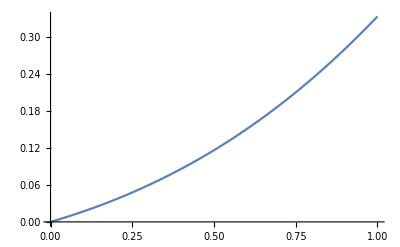

```mathematica
Plot[r*1/(1+2Exp[1-r]),{r,0,1}]
```